```mathematica
ex82= Import["/Volumes/GoogleDrive/My Drive/TexasA&M/4-Semester/327_328-PHYS/8_Lab/table/t2.csv"];
```

```mathematica
TableForm[ex82]
```

Frequency (Hz) | Uncertainty (Hz) | V_a | Uncertainty(V_a) | V_b (uV) | Uncertainty(V_b) | Actual | Predicted | Residuals
98.52 | 1 | 0.6694 | 1 | 4.41 | 1 | 6563.88 | 4553.94 | 2009.94
250.4 | 1 | 0.6689 | 1 | 4.42 | 1 | 6583.68 | 4650.56 | 1933.12
499.1 | 1 | 0.6682 | 1 | 4.43 | 1 | 6605.49 | 4808.78 | 1796.71
745.1 | 1 | 0.6667 | 1 | 4.41 | 1 | 6590.46 | 4965.28 | 1625.18
1000 | 1 | 0.6641 | 1 | 4.37 | 1 | 6556.25 | 5127.44 | 1428.81
4847 | 1 | 0.6672 | 1 | 2.075 | 1 | 3098.63 | 7574.83 | -4476.2
20860 | 1 | 0.6658 | 1 | 9.509 | 1 | 14229.8 | 17762. | -3532.2
39070 | 1 | 0.6624 | 1 | 17.97 | 1 | 27029.3 | 29346.9 | -2317.52
59510 | 1 | 0.6598 | 1 | 27.54 | 1 | 41587.2 | 42350.4 | -763.238
80150 | 1 | 0.6584 | 1 | 36.72 | 1 | 55567.4 | 55481.2 | 86.2763
99680 | 1 | 0.6575 | 1 | 46.27 | 1 | 70115.1 | 67905.8 | 2209.28

```mathematica
col1 = ex82[[All, 1]][[2 ;; 12]];
col2 = ex82[[All, 2]][[2 ;; 12]];
col3 = ex82[[All, 3]][[2 ;; 12]];
col4 = ex82[[All, 4]][[2 ;; 12]];
col5 = ex82[[All, 5]][[2 ;; 12]];
col6 = ex82[[All, 6]][[2 ;; 12]];
col7 = ex82[[All, 7]][[2 ;; 12]];
col8 = ex82[[All, 8]][[2 ;; 12]];
col9 = ex82[[All, 9]][[2 ;; 12]];
```

```mathematica
r1 = 0.99634 * 1000; (*resistor-1*)
col10 = col5 / col3;
colR = r1 * col10; (*Resistance*)
colU = col6 / col2; (*Uncertainty*)
```

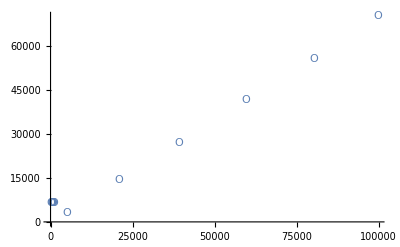

FittedModel[4491.26+0.636181 x]

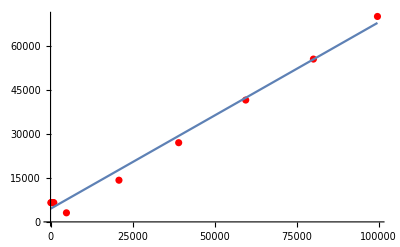
-Graphics-ResistanceFrequency (Hz)

4491.26+0.636181 x

```mathematica
(*Plot Chart*)
ex8Pair = {col1, colR};
ex8Tuple = Transpose[ex8Pair];
ListPlot[ex8Tuple, PlotMarkers->{"O"}]

(**************************************)
(**************************************)
(**************************************)
(**************************************)


(*Weighted Least Square Fit*)
sim=Flatten[MapThread[Function[{a},{#1[[1]],a}]/@RandomVariate[NormalDistribution[#1[[2]],#2],200]&,{ex8Tuple,colU}],1];
fit2=LinearModelFit[ex8Tuple,x,x,Weights->1/colU]
Labeled[
Show[
ListPlot[ex8Tuple,PlotStyle->Red],
Plot[{fit2[x]},{x,0,ex8Tuple[[-1,1]]}]   ],
{"Resistance", "Frequency (Hz)"},
{Left, Bottom},
RotateLabel->True
]
Normal@fit2
```

```mathematica
4491.260539611512+0.6361814833801359 x
```

4491.26+0.636181 x

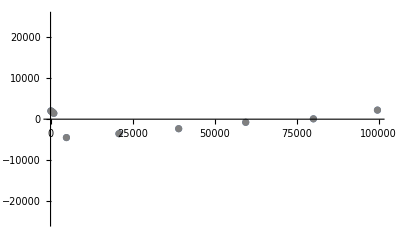
-Graphics-V.b2 (mV).b2Frequency (kHz)

```mathematica
(**************************************)
(**************************************)
(**************************************)
(**************************************)

(*Residual Graph*)

ex8ErrPair = {col1, col9};
ex8ErrTuple = Transpose[ex8ErrPair];
ex8Err2Trip = {col1, col9, col4};
ex8ErrT2 = Transpose[ex8Err2Trip];

Needs["ErrorBarPlots`"]
Labeled[
	Show[
	ListPlot[ex8ErrTuple, PlotRange->{-25000, 25000}],     (*Note the Range*)
	ErrorListPlot[ex8ErrT2,PlotStyle->Gray]
   ],
{"V.b2 (mV).b2", "Frequency (kHz)"},
{Left, Bottom},
RotateLabel->True
]
```